## Configuration

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pwrzosek/Documents/GitHub/Direct_Greens_Function/rotsaw/mathematica

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,NumberForm[x,{Infinity,1}],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

```mathematica
SetOptions[LinTicks,TickLengthScale->2];
SetOptions[MaTeX,Magnification->1.4,"Preamble"->{"\\usepackage{xcolor}"}];
SetOptions[ListDensityPlot,
InterpolationOrder->0,
ClippingStyle->Black,
ColorFunction->ColorData[{"SunsetColors","Reverse"}],
ColorFunctionScaling->True,
AspectRatio->3/4,
ImageSize->400,
FrameStyle->Directive[Black,20,FontFamily->"CMU Serif"],
FrameTicksStyle->Directive[Black,20,FontFamily->"CMU Serif"],
LabelStyle->Directive[Black,20,FontFamily->"CMU Serif"],
FrameLabel->{MaTeX["J/t"],MaTeX["\\omega/t"]},
PlotLegends->Placed[BarLegend[{ColorData[{"SunsetColors","Reverse"}],{0,1}},LegendMarkerSize->170,LegendLayout->"Row","Ticks"->({#,(opt={"0","0.3"};MaTeX[opt[[#+1]]])}&/@{0,1}),"TickSide"->Right,TicksStyle->Directive[Black,Thickness[0.005]],"FrameStyle"->Directive[Black,Thickness[0.005]],LabelStyle->Directive[Black,20,FontFamily->"CMU Serif"]],{0.70,0.85}]
];
```

## Main

```mathematica
Grot[w_,J_]:=Module[
{
result
},(
result=0;
Do[result=1/(w-2n J-3result),{n,Min[1000,Round[10/J]],2,-1}];
Return[result];
)];
G[w_,J_]:=1/(w-2J-4Grot[w,J]);
G3[w_,J_]:=1/(w-2J-3Grot[w,J]);
```

```mathematica
A[f_,w_,J_]:=-Im[f[w+0.05I,J]]/Pi;
```

```mathematica
AG=Table[A[G,x,y],{x,-6,14,0.01},{y,0.01,2,0.01}];
```

```mathematica
AGr=Table[A[Grot,x,y],{x,-6,14,0.01},{y,0.01,2,0.01}];
```

```mathematica
gsSearch[sf_]:=Module[
{
result={}
},(
Do[AppendTo[result,Position[s,Max[s]][[1,1]]],{s,Transpose[sf]}];
Return[result];
)]
```

```mathematica
align[sf_,gs_]:=Module[
{
result={}
},(
Do[
AppendTo[result,
Join[sf[[gs[[iJ]];;-1,iJ]],
Table[0,gs[[iJ]]-1]
]
],
{iJ,Length[gs]}];
Return[result//Transpose];
)];
```

```mathematica
gs=gsSearch[AG];
```

```mathematica
AGal=align[AG,gs];
```

```mathematica
AGral=align[AGr,gs];
```

```mathematica
AG3=Table[A[G3,x,y],{x,-6,14,0.01},{y,0.05,2,0.01}];
```

```mathematica
AG3al=align[AGr,gsSearch[AG3]];
```

```mathematica
dp=ListDensityPlot[AGral,DataRange->{{0.01,2},{0,20}},
PlotRange->{{0,2},{0,10},{0,0.5}},
FrameLabel->MaTeX@{"J/t","\\omega/t"},
ColorFunction->ColorData[{"SunsetColors","Reverse"}],
ClippingStyle->Black,
AspectRatio->3/4,
FrameTicks->{
{LinTicks[0,10,2,10,TickLabelFunction->tlf],LinTicks[0,10,2,10,ShowTickLabels->False]},
{LinTicks[0,2,0.4,4,TickLabelFunction->tlf],LinTicks[0,2,0.4,4,ShowTickLabels->False]}
},
Epilog->{
Inset[MaTeX["A(\\omega)",Magnification->1.5],Scaled[{0.35,0.85}],{0,0}]
},
InterpolationOrder->0
]
```

-Graphics-

```mathematica
dp3=ListDensityPlot[AG3al,DataRange->{{0.01,2},{0,20}},
PlotRange->{{0,2},{0,10},{0,0.5}},
FrameLabel->MaTeX@{"J/t","\\omega/t"},
ColorFunction->ColorData[{"SunsetColors","Reverse"}],
ClippingStyle->Black,
AspectRatio->3/4,
FrameTicks->{
{LinTicks[0,10,2,10,TickLabelFunction->tlf],LinTicks[0,10,2,10,ShowTickLabels->False]},
{LinTicks[0,2,0.4,4,TickLabelFunction->tlf],LinTicks[0,2,0.4,4,ShowTickLabels->False]}
},
Epilog->{
Inset[MaTeX["A(\\omega)",Magnification->1.5],Scaled[{0.35,0.85}],{0,0}]
},
InterpolationOrder->0
]
```

-Graphics-

```mathematica
gsGral=gsSearch[AGral]/100//N;
```

```mathematica
gsGralRev=Table[{0.01+(n-1)0.01,gsGral[[n]]},{n,Length[gsGral]}];
```

```mathematica
gsf=FindFormula[gsGralRev[[70;;-1]]]
```

2.87983 #1&

```mathematica
gsf2=FindFormula[gsGralRev]
```

2.87971 #1&

```mathematica
lf[x_,a_:2,b_:0]:=a x+b
```

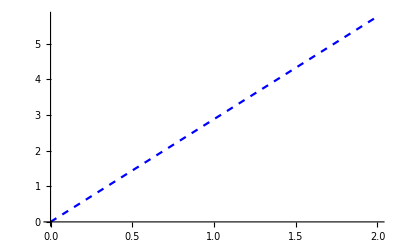

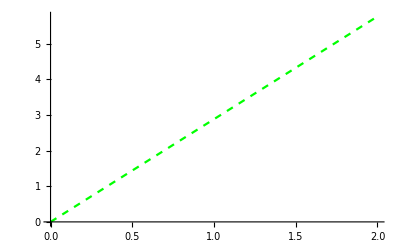

```mathematica
lp1=Plot[{gsf[x]},{x,0.0,2},PlotStyle->{Dashed,Blue}]
lp2=Plot[{gsf2[x]},{x,0,2},PlotStyle->{Dashed,Green}]
```

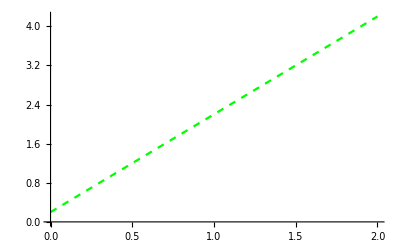

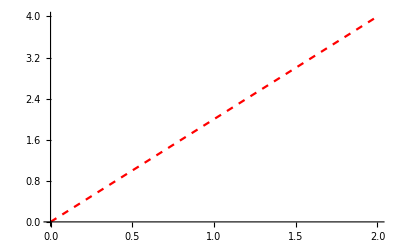

```mathematica
lp3=Plot[{lf[x,2,0.2]},{x,0,2},PlotStyle->{Dashed,Green}]
lp4=Plot[{lf[x]},{x,0,2},PlotStyle->{Dashed,Red}]
```

```mathematica
Module[
{
holeFillingColor=Lighter[Blue],(*Darker[Blend[{Blue,Darker[Cyan]},0.5]];*)
magnonFillingColor=Lighter[Red],
eraserColor=White,
h=0.55,
hw=0.2,
r=0.1,
lineThickness=0.05
},(
GetLattice[depths_:{6,1},scaling_:1]:=Module[
{vertices,coordinates,edges,parent,vertex,index,angle,SpanLattice},(

SpanLattice[d_,depth_,lastAngle_,s_,localParent_]:=Module[{localVertex,localAngle,it},(
If[d<depth,(
For[it=1,it<Length[depths],it++,(
localVertex=vertices[[-1]]+1;
localAngle=2Pi it/Length[depths];
AppendTo[vertices,localVertex];
AppendTo[coordinates,coordinates[[localParent]]+
s*{Cos[lastAngle-Pi+localAngle],Sin[lastAngle-Pi+localAngle]}];
AppendTo[edges,localParent<->localVertex];
SpanLattice[d+1,depth,lastAngle-Pi+localAngle,s*scaling,localVertex];
)]
)]
)];

vertices={1};
coordinates={{0,0}};
edges={};
index=0;
parent=vertices[[1]];
Do[(
vertex=vertices[[-1]]+1;
angle=2Pi index/Length[depths];
AppendTo[vertices,vertex];
AppendTo[coordinates,coordinates[[parent]]+1{Cos[angle],Sin[angle]}];
AppendTo[edges,parent<->vertex];
SpanLattice[1,depth,angle,scaling,vertex];
index+=1;
),
{depth,depths}];
{vertices,coordinates,edges})];

{v,c,e}=GetLattice[{3,3,3},1/Sqrt[3]];
g=Graph[v,e,VertexCoordinates->c,VertexShapeFunction->None,EdgeStyle->Thick,VertexSize->0,VertexLabels->"Name"];

a[x_,y_,h_,color_:Black]:={Thickness[0.0075],color,Arrowheads[0.06],Arrow[{{x,y-h/2},{x,y+h/2}}]};
d[x_,y_,r_,color_,ef_:{Thickness[0.01],Black}]:={EdgeForm[ef],color,Disk[{x,y},r]};
rc[x_,y_,r_,color_,ef_:{Black}]:={EdgeForm[ef],Lighter[color],Disk[{x,y},r]};
er[x_,y_,dx_,dy_,ef_:{White}]:={EdgeForm[ef],eraserColor,Rectangle[{x-dx/2,y-dy/2},{x+dx/2,y+dy/2}]};

bethe[holePath_,step_]:=(
spins={1};
Do[(
AppendTo[spins,-spins[[e[[it-1,1]]]]]
),{it,Complement[v,{1}]}];

hlEdge={};
Do[(
Do[(
If[edge[[1]]==it,
AppendTo[hlEdge,
Line[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{it,holePath[[1;;(step-1)]]}]
),{edge,e}];

hlPath={};
Do[(
Do[(
If[edge==holePath[[it]]<->holePath[[it+1]]||edge==holePath[[it+1]]<->holePath[[it]],
AppendTo[hlPath,
Arrow[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{it,Length[holePath[[1;;step]]]-1}]
),{edge,e}];

hlJumps={};
Do[(
If[edge[[1]]==holePath[[step]],
AppendTo[hlJumps,
Line[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{edge,e}];

hole={d[c[[holePath[[step]],1]],c[[holePath[[step]],2]],r,holeFillingColor]};

oldHole={d[c[[holePath[[1]],1]],c[[holePath[[1]],2]],r,White,{Thickness[0.01],Black,Dashed}]};

baseline=Table[Line[{{c[[e[[n-1,1]],1]],c[[e[[n-1,1]],2]]},{c[[n,1]],c[[n,2]]}}],{n,2,v[[-1]]}];

hlEdge=Complement[hlEdge,hlPath];
(*baseline=Complement[baseline,hlJumps];*)
baseline=Complement[baseline,hlPath];

Join[
{{Opacity[1,Gray],Thickness[lineThickness],baseline}},
(*{{Opacity[0.6,Darker[Green]],Thickness[lineThickness],hlJumps}},*)
{{Opacity[0.6,Blue//Lighter],Thickness[lineThickness],hlPath}}
]
);

b1=Graphics[{bethe[{1},1]},Frame->False,PlotRange->All,PlotRangeClipping->True]
)];
bethe3=Show[b1,ImageSize->60]
```

-Graphics-

```mathematica
Module[
{
holeFillingColor=Lighter[Blue],(*Darker[Blend[{Blue,Darker[Cyan]},0.5]];*)
magnonFillingColor=Lighter[Red],
eraserColor=White,
h=0.55,
hw=0.2,
r=0.1,
lineThickness=0.04
},(
GetLattice[depths_:{6,1},scaling_:1]:=Module[
{vertices,coordinates,edges,parent,vertex,index,angle,SpanLattice},(

SpanLattice[d_,depth_,lastAngle_,s_,localParent_]:=Module[{localVertex,localAngle,it},(
If[d<depth,(
For[it=1,it<Length[depths],it++,(
localVertex=vertices[[-1]]+1;
localAngle=2Pi it/Length[depths];
AppendTo[vertices,localVertex];
AppendTo[coordinates,coordinates[[localParent]]+
s*{Cos[lastAngle-Pi+localAngle],Sin[lastAngle-Pi+localAngle]}];
AppendTo[edges,localParent<->localVertex];
SpanLattice[d+1,depth,lastAngle-Pi+localAngle,s*scaling,localVertex];
)]
)]
)];

vertices={1};
coordinates={{0,0}};
edges={};
index=0;
parent=vertices[[1]];
Do[(
vertex=vertices[[-1]]+1;
angle=2Pi index/Length[depths];
AppendTo[vertices,vertex];
AppendTo[coordinates,coordinates[[parent]]+1{Cos[angle],Sin[angle]}];
AppendTo[edges,parent<->vertex];
SpanLattice[1,depth,angle,scaling,vertex];
index+=1;
),
{depth,depths}];
{vertices,coordinates,edges})];

{v,c,e}=GetLattice[{3,3,3,3},1/Sqrt[5]];
g=Graph[v,e,VertexCoordinates->c,VertexShapeFunction->None,EdgeStyle->Thick,VertexSize->0,VertexLabels->"Name"];

a[x_,y_,h_,color_:Black]:={Thickness[0.0075],color,Arrowheads[0.06],Arrow[{{x,y-h/2},{x,y+h/2}}]};
d[x_,y_,r_,color_,ef_:{Thickness[0.01],Black}]:={EdgeForm[ef],color,Disk[{x,y},r]};
rc[x_,y_,r_,color_,ef_:{Black}]:={EdgeForm[ef],Lighter[color],Disk[{x,y},r]};
er[x_,y_,dx_,dy_,ef_:{White}]:={EdgeForm[ef],eraserColor,Rectangle[{x-dx/2,y-dy/2},{x+dx/2,y+dy/2}]};

bethe[holePath_,step_]:=(
spins={1};
Do[(
AppendTo[spins,-spins[[e[[it-1,1]]]]]
),{it,Complement[v,{1}]}];

hlEdge={};
Do[(
Do[(
If[edge[[1]]==it,
AppendTo[hlEdge,
Line[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{it,holePath[[1;;(step-1)]]}]
),{edge,e}];

hlPath={};
Do[(
Do[(
If[edge==holePath[[it]]<->holePath[[it+1]]||edge==holePath[[it+1]]<->holePath[[it]],
AppendTo[hlPath,
Arrow[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{it,Length[holePath[[1;;step]]]-1}]
),{edge,e}];

hlJumps={};
Do[(
If[edge[[1]]==holePath[[step]],
AppendTo[hlJumps,
Line[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{edge,e}];

hole={d[c[[holePath[[step]],1]],c[[holePath[[step]],2]],r,holeFillingColor]};

oldHole={d[c[[holePath[[1]],1]],c[[holePath[[1]],2]],r,White,{Thickness[0.01],Black,Dashed}]};

baseline=Table[Line[{{c[[e[[n-1,1]],1]],c[[e[[n-1,1]],2]]},{c[[n,1]],c[[n,2]]}}],{n,2,v[[-1]]}];

hlEdge=Complement[hlEdge,hlPath];
(*baseline=Complement[baseline,hlJumps];*)
baseline=Complement[baseline,hlPath];

Join[
{{Opacity[1,Gray],Thickness[lineThickness],baseline}},
(*{{Opacity[0.6,Darker[Green]],Thickness[lineThickness],hlJumps}},*)
{{Opacity[0.6,Blue//Lighter],Thickness[lineThickness],hlPath}}
]
);

b2=Graphics[{bethe[{1},1]},Frame->False,PlotRange->All,PlotRangeClipping->True]
)];
bethe4=Show[b2,ImageSize->80]
```

-Graphics-

```mathematica
pt1=Show[{dp3,lp4},Inset[bethe3,Scaled[0.5,0.5],{0,0}]]
```

Show::gcomb: Could not combine the graphics objects in Show[{Legended[-Graphics-, Placed[BarLegend[{ColorDataFunction[{1, 0}, <>], {0, 1}}, <<11>>], {0.7, 0.85}, Identity]], -Graphics-}, Inset[<<3>>]].

Show[{-Graphics-,-Graphics-},Inset[-Graphics-,Scaled[0.5,0.5],{0,0}]]

```mathematica
pt2=Show[{dp,lp4,lp2}]
```

-Graphics-

```mathematica
(*Export["perfect_linear.png",pt1]
Export["linear.png",pt2]*)
```

```mathematica
Table[Min[1000,Round[10/J]],{J,0.01,1,0.01}]
```

{1000,500,333,250,200,167,143,125,111,100,91,83,77,71,67,62,59,56,53,50,48,45,43,42,40,38,37,36,34,33,32,31,30,29,29,28,27,26,26,25,24,24,23,23,22,22,21,21,20,20,20,19,19,19,18,18,18,17,17,17,16,16,16,16,15,15,15,15,14,14,14,14,14,14,13,13,13,13,13,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,10,10,10,10,10}